```mathematica
<<peeters`
peeters`setGitDir["../project/figures/GAelectrodynamics"]
```

peeters`

/Users/pjoot/project/figures/GAelectrodynamics

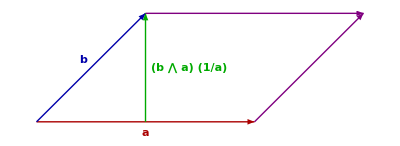

```mathematica
ClearAll[o, a, b, i, j, bb, bbi, c2v, bperp, bproj, brej, g]
o = {0,0};
a = {2,0};
b = {1,1};
bb = 1 + I;
i = {1,0};
j = {0,1};
bbi = bb * I;
c2v[z_] := {z//Re, z//Im}
bperp = (bbi // c2v )/Sqrt[2];
bproj = (b . a) a/((Norm[a])^2);
brej = b - bproj;
fs = Style[#, {Bold, Larger}] &;

g = Graphics[{
Thick,
Red // Darker,
Arrow[{o,a}], 
Text["a" //fs, a/2 - 0.1j ],
Blue// Darker,
Arrow[{o,b}],
Text["b" //fs, b/2 +0.1 bperp ],
Green // Darker,
Arrow[{bproj, b}],
Text["(b ⋀ a) (1/a)" //fs, bproj + brej/2 + 0.4 i ],
Purple,
Arrow[{a, a+ b}],
Arrow[{b,a+b}]
}]
```

```mathematica
(*https://stackoverflow.com/questions/4641512/how-to-install-new-packages-for-mathematica*)
```

```mathematica
$UserBaseDirectory
```

/Users/pjoot/Library/Mathematica

```mathematica
peeters`exportForLatex["parallelogramAreaFig1",g]
```

{parallelogramAreaFig1.eps,parallelogramAreaFig1pn.png}